# VAJE IZ RAČUNALNIŠKA ORODJA V MATEMATIKI

1. NALOGA

V Mathematici predstavimo daljico v obliki Daljica[AA_, BB_], kjer sta AA in BB točki predstavljeni s parom koordinat v obliki {x, y}. 
 
 Sestavi naslednje funkcije:
- Dolzina[Daljica[AA_, BB_]], ki vrne dolžino daljice.
- EnacbaNosilke[Daljica[AA_, BB_]], ki rne enačbo premice nosilke daljice. Primer, za daljico d kot zgoraj je enačba nosilke y == -x/2 + 1/2.
- Slika[Daljica[AA_, BB_]], ki vrne grafični objekt Line, kateri predstavlja daljico.
- Narisi[d__Daljica], ki za eno ali več podanih daljic le-te izriše.

```mathematica
d = Daljica [{-1, 1}, {3, -1}]
```

Daljica[{-1,1},{3,-1}]

```mathematica
d2 = Daljica[{-1, -1}, {3, 1}]
```

Daljica[{-1,-1},{3,1}]

```mathematica
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,2},{3,0}]

Dolzina[Daljica[AA_, BB_]], ki vrne dolžino daljice.

```mathematica
Dolzina [Daljica[AA_, BB_]] := Norm[BB - AA]
```

```mathematica
Dolzina[d]
```

2 √5

Slika[Daljica[AA_, BB_]], ki vrne grafični objekt Line, kateri predstavlja daljico.

```mathematica
Slika[Daljica[AA_, BB_]] := Line[{AA, BB}]
```

Narisi[d__Daljica], ki za eno ali več podanih daljic le - te izriše.

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
```

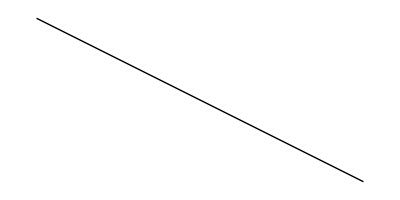

```mathematica
Narisi[d]
```

```mathematica
ClearAll[x, y]
```

EnacbaNosilke[Daljica[AA_, BB_]], ki rne enač̌bo premice nosilke daljice. Primer, za daljico d kot zgoraj je enač̌ba nosilke y == -x/2 + 1/2.

```mathematica
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, x2, y1, y2, k, n},
{x1, y1} = AA;
{x2, y2} = BB;

k = (y2 - y1)/ (x2 - x1);
n = n /. First[Solve[y1 == k*x1 + n, n]];
y == k * x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

# 2. NALOGA

Sestavi funkcijo Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]], ki vrne presečišče daljic, če se sekata, oziroma prazen seznam ({}).

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] := Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0,  r ≤ 1, s ≥ 0,  s ≤ 1}, {r, s}];
If[resitev == {}, 
{},
First [AA + r (BB - AA) /. resitev ]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

# 3. NALOGA

Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik.

Primer
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}].

Ker gre za sklenjen mnogokotnik, predvidevamo, da ima ta povezave med zaporednimi točkami ter od zadnje do prve točke. Sestavi naslednje funkcije:

```mathematica
m1=Mnogokotnik[{0,0}, {1, 1}, {0,3}, {-1, 2}]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

```mathematica
m2=Mnogokotnik[{1, 3}, {0, 2}, {2, 2}, {-1, 0}]
```

Mnogokotnik[{1,3},{0,2},{2,2},{-1,0}]

```mathematica
Stranice[{AA_, BB_, CC_, DD_}] := {{AA, BB}, {BB, CC}, {CC, DD}, {AA, DD}}
```

Slika[Mnogokotnik[t__]], ki predstavi mnogokotnik s pomočjo grafičnega objekta Line.Naj - prej sestavi nov seznam točk, ki vključuje obstoječe točke mnogokotnika ter še ponovljeno prvo.Pozor : pazi, da ne izbrišeš obstoječe funkcije za sliko daljice!

```mathematica
Slika[Mnogokotnik[t__]]:=Line[{t}]
```

```mathematica
Slika[m1]
```

Line[{{0,0},{1,1},{0,3},{-1,2}}]

```mathematica
m1 = Append[m1, First[m1]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

Narisi[m__Mnogokotnik], ki nariše enega ali več mnogokotnikov. Pazi, pri risanju moraš narediti tudi daljico od zadnje do začetne točke. Premisli, kako iz obstoječega seznama točk sestaviš nov seznam, ki daljši za eno točko, t.j. ponovljeno prvo točko (Namig: funkciji Append ter First na seznamih.)

```mathematica
Narisi[m__Mnogokotnik]:= Graphics[Map[Slika, List[m]]]
```

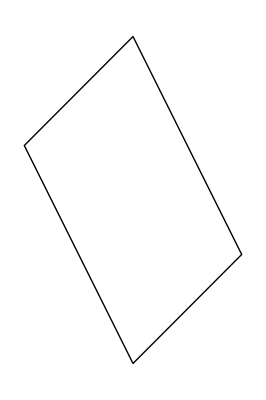

```mathematica
Narisi[m1]
```

PravilniNKotnik[n_, r_], ki nariše pravilni n-kotnik s središčem v točki (0, 0) in s točkami na krožnici z radijem r, pri čemer je ena točka v (r, 0). 
Naming: uporabi funkcijo Table in upoštevaj,
da se točke nahajajo na koordinatah (rcos(2π∗i,rsin(2π∗i)) za i = 0,...,n−1. Izriši :
p5 = PravilniNKotnik[5, 2]

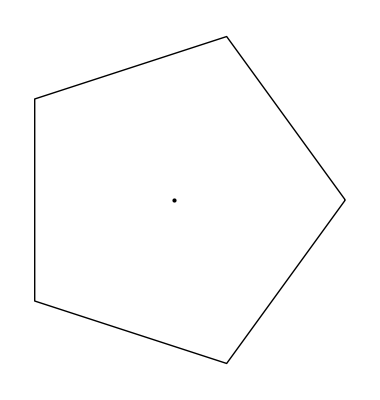

```mathematica
PravilniNKotnik[n_,r_]:=Graphics[{Line[Table[{r*Cos[(2 Pi*i)/n],r*Sin[(2 Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5=PravilniNKotnik[5,2]
```

Nadgradi prejšnjo funkcijo v PravilniNKotnik[n_, r_, phi_], ki zgornji pravilni n-kotnik zavrti za kot phi. Premisli, kako je treba nadgraditi formulo za posamezno točko, da se premakne za kot phi. Rezultat uporabi v kombinaciji s funkcijo Manipulate in interaktivno demonstriraj rotacijo.

```mathematica
PravilniNKotnik[n_, r_, phi_]:= Manipulate[Graphics[
{Line[Table[{r*Cos[(2Pi*i + x)/n],r*Sin[(2Pi*i + x)/n]},{i,0,n}]],Point[{0,0}]}], {x, 0, Pi}]
```

```mathematica
Manipulate[Narisi[PravilniNKotnik[5,2,phi]], {phi, 0, Pi}
```

```mathematica
PravilniNKotnik[5, 2, Pi]
```

PravilniNKotnik[5,2,π]

Daljice[Mnogokotnik[t__]], ki vrne seznam daljic, ki tvorijo mnogokotnik. Uporabi funkcijo Partition. V dokumentaciji preveri, kako deluje funkcija ter kako se uporablja zamikanje. 

Oglej si, kaj naredita naslednja ukaza:
Partition[{1, 2, 3, 4, 5} , 2]
Partition[{1, 2, 3, 4, 5} , 2, 1]

```mathematica
Daljice[Mnogokotnik[t__]]:=Partition[{t}, {2, 2}, 1]
```

```mathematica
m1
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

```mathematica
Daljice[m1]
```

{{{{0,0},{1,1}}},{{{1,1},{0,3}}},{{{0,3},{-1,2}}},{{{-1,2},{0,0}}}}

# 4. NALOGA

Sestavi funkcijo Presek[m_Mnogokotnik, d_Daljica], ki izračuna presečišča mnogokotnika in daljice.Pri tem uporabi že napisane funkcije ter pazi, da rezultat ne istih presečišč večkrat.Poskusi uporabiti vgrajeni funkciji Select in DeleteDuplicates.Pomagaj si z naslednjimi primeri.Funkcijo lahko definiramo tudi na naslednji način (namesto argumenta damo znak #, na koncu definicije pa dodamo znak &.

Presek[m_Mnogokotnik, d_Daljica]

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]] := Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0,  r ≤ 1, s ≥ 0,  s ≤ 1}, {r, s}];
If[resitev == {}, 
{},
First [AA + r (BB - AA) /. resitev ]
]
]
```

```mathematica
d1 = Daljica[{-1,1},{3,-1}];
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}];
m = Append[m1, m1[[1]]]
seznamDaljic = Map[Daljica, Daljice[m]]
Daljice[Mnogokotnik[t__]] := Partition[{t},2,1]
Daljice[m]
Daljice1 = Partition[Flatten[Daljice[m]], 2, 2]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

{{{0,0},{1,1}},{{1,1},{0,3}},{{0,3},{-1,2}},{{-1,2},{0,0}}}

{{0,0},{1,1},{1,1},{0,3},{0,3},{-1,2},{-1,2},{0,0}}

```mathematica
PresekBrezSeznama = Presek1[m__Mnogokotnik, d__Daljica] :=  
	For[i = 1, i <= Length[Daljice[m]], i++, Print[Presek[Daljica[Daljice[m][[i]][[1]], Daljice[m][[i]][[2]]], d]]]
```

```mathematica
Presek1[m, d1]
```

{1/3,1/3}

{}

{}

{-1/3,2/3}

# 5. NALOGA

Spodnja funkcija izračuna (uporabi) funkcijo f na vseh parih iz dveh seznamov.
VsiPari[f_, sez1_, sez2_] := Flatten[Outer[f, sez1, sez2], 1]
VsiPari[f, {1, 2, 3}, {a, b}]
{f[1, a], f[1, b], f[2, a], f[2, b], f[3, a], f[3, b]}

Preuči, kaj točno naredita funkciji OUTER in FLATTEN. Poglej v pomoč in preizkusi na primerih

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
VsiPari[k,{2,3,4},{7,3,5}]
```

{k[2,7],k[2,3],k[2,5],k[3,7],k[3,3],k[3,5],k[4,7],k[4,3],k[4,5]}

```mathematica
VsiPari[f,{{1,2},{3,4}},{{aa,bb},{dd,cc}}]
```

{{{f[1,aa],f[1,bb]},{f[1,dd],f[1,cc]}},{{f[2,aa],f[2,bb]},{f[2,dd],f[2,cc]}},{{f[3,aa],f[3,bb]},{f[3,dd],f[3,cc]}},{{f[4,aa],f[4,bb]},{f[4,dd],f[4,cc]}}}

```mathematica
Outer[f,{2,4,3,{5},9}]
```

{f[2],f[4],f[3],{f[5]},f[9]}

```mathematica
Flatten[Outer[f,{2,4,3,{5},9}],1]
```

{f[2],f[4],f[3],f[5],f[9]}

```mathematica
? Outer
```

Outer[f,list_1,list_2,…] gives the generalized outer product of the list_i, forming all possible combinations of the lowest-level elements in each of them, and feeding them as arguments to f. 
Outer[f,list_1,list_2,…,n] treats as separate elements only sublists at level n in the list_i. 
Outer[f,list_1,list_2,…,n_1,n_2,…] treats as separate elements only sublists at level n_i in the corresponding list_i.

```mathematica
? Flatten
```

Flatten[list] flattens out nested lists. 
Flatten[list,n] flattens to level n. 
Flatten[list,n,h] flattens subexpressions with head h. 
Flatten[list,{{s_11,s_12,…},{s_21,s_22,…},…}] flattens list by combining all levels s_ij to make each level i in the result.

Sestavi funkcijo Presek[m1_Mnogokotnik, m2_Mnogokotnik], ki poišče presek dveh pravokotni - kov.Uporabi funkcijo VsiPari.

```mathematica
Presek[m1_Mnogokotnik, m2_Mnogokotnik]:=
For[j = 1, j ≤Length[Daljice[m2]], j++, 
For[i=1, i<Length[Daljice[m1]], i++,
Print[Presek[Daljica[Daljice[m1][[i]][[1]], Daljice[m1][[i]][[2]]],
 Daljica[Daljice[m2][[i]][[1]], Daljice[m2][[i]][[2]]]]]]]
```

```mathematica
Presek[m1, m2]
```

{}

{1/2,2}

{}

{1/2,2}

{}

{1/2,2}

# 6. NALOGA

Izberi eno izmed nalog iz snovi pri linearni algebri in jo reši.Opiši potek in čim več računskega dela prepusti Mathematici.Če je možno, rezultate predstavi še grafično.

Imamo trikotnik s točkami A (2, 4), B (1, 5), C (3, 2). Izračunaj enotske vektorje AB, BC in CA, ter nariši ta trikotnik.

```mathematica
AA={2,4}
```

{2,4}

```mathematica
BB={1,5}
```

{1,5}

```mathematica
CC={2,3}
```

{2,3}

```mathematica
Vektor[A_,B_]:=Norm[A-B]
```

Definirali smo točke trikotnika in zapisali funkcijo, ki izračuna dolžino vektorja (razdalja med točkama je enaka dolžini razlike krajevnih vektorjev obeh točk).

```mathematica
EnotskiVektor[A_,B_]:=(B-A)/Vektor[A,B]
```

Funkcija za izračun enotskega vektorja. e = a/(|a|)

```mathematica
EnotskiVektor[AA,BB]
EnotskiVektor[BB,CC]
EnotskiVektor[CC,AA]
```

{-1/(√2),1/(√2)}

{1/(√5),-2/(√5)}

{0,1}

```mathematica
trikotnik = {AA,BB,CC}
tocke = Append[trikotnik,trikotnik[[1]]]
```

{{2,4},{1,5},{2,3}}

{{2,4},{1,5},{2,3},{2,4}}

Točke damo v skupen seznam. Na koncu dodamo še prve točke da bomo lahko lik izrisali.

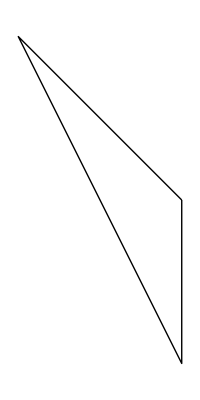

```mathematica
NarisiTrikotnik[tocke_] := Graphics[Line[tocke]]
NarisiTrikotnik[tocke]
```

Funkcija vzame seznam točk, jih spremeni v daljice in te narise.